```mathematica
list={1,0,0,1,1,0,1}
```

{1,0,0,1,1,0,1}

```mathematica
Flatten[Delete[Prepend[IntegerDigits[123,2],Take[list,-1]],-1]]
```

{1,1,1,1,1,0,1}

```mathematica
2^^1100110
```

102

```mathematica
Last[list]
```

1

```mathematica
Delete[list,-1]
```

{1,0,0,1,1,0}

```mathematica
FromDigits[Flatten[Delete[Prepend[IntegerDigits[123,2],Take[IntegerDigits[123,2],-1]],-1]],2]
```

125

```mathematica
IntegerDigits[123,2]
```

{1,1,1,1,0,1,1}

```mathematica
2^^1111011+2^^1111101
```

248

```mathematica
BaseForm[%,2]
```

11111000_2

```mathematica
reorderpal[x_Integer,y_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(FromDigits[Flatten[Delete[Prepend[IntegerDigits[#,2],Take[IntegerDigits[#,2],-1]],-1]],2]+#)&,x,IntegerDigits[IntegerReverse[#,2],2]=!=IntegerDigits[#,2]&,1,y],2]]]
```

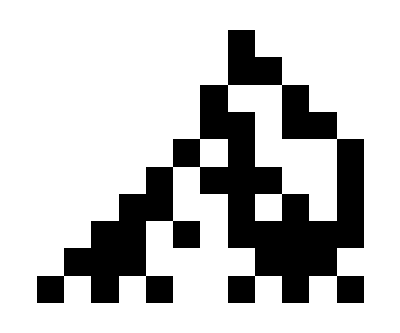

```mathematica
reorderpal[16,50]
```

```mathematica
reorderrep[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestList[(FromDigits[Flatten[Delete[Prepend[IntegerDigits[#,2],Take[IntegerDigits[#,2],-z]],-z]],2]+#)&,x,y],2]]]
```

```mathematica
reorderrep[776,100,1]
```

-Graphics-

```mathematica
reorderpal2[x_Integer,y_Integer,z_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestWhileList[(FromDigits[Flatten[Delete[Prepend[IntegerDigits[#,2],Take[IntegerDigits[#,2],-z]],-z]],2]+#)&,x,IntegerDigits[IntegerReverse[#,2],2]=!=IntegerDigits[#,2]&,1,y],2]]]
```

```mathematica
Animate[reorderpal2[1024,100,x],{x,1,5,1}]
```